%%%Equation for V[r]-VLX[r]

```mathematica
EEq[r]:=(-12 gam[r]^2 (r-2 m[r]) (-3 m[r]+r (2+m'[r]))+2 r gam[r] (r-2 m[r]) (m[r] (23-8 gam'[r])+r (-6+4 gam'[r]-11 m'[r]+r m''[r]))+r^2 (8 m[r]^2 (6 gam'[r]-r gam''[r])+4 r m[r] (-1+2 m'[r]-2 gam'[r] (5+2 m'[r])+2 r gam''[r]-r m''[r])+r^2 (2 (1+4 gam'[r]-2 m'[r]) (1+m'[r])-2 r gam''[r]+r (1+2 m'[r]) m''[r])))/(2 r^5 gam[r])
```

%%Mass-function used

```mathematica
m[r]:=1-27/(32 r^3);
m'[r]:=D[m[r],r];
m''[r]:=D[m'[r],r];
Derivative[3][m][r]:=D[m''[r],r];
Derivative[4][m][r]:=D[Derivative[3][m][r],r]
```

%%%ANSATZ for the gam-function

```mathematica
FF[r]:= 1 + (2 m'[r] - r m''[r])/2
```

```mathematica
gam[r]:= - (r^2/(2 r + 3 m[r] - r  m'[r])) FF[r]
```

```mathematica
gam'[r]:=D[gam[r],r];
gam''[r]:=D[gam'[r],r]
```

%%%Copiyng and redefining functions (in principle a short cut possible)

```mathematica
G2[r]:=EEq[r]
```

```mathematica
G3[r_]=G2[r]
```

-1/(2 (1+243/(32 r^4)) r^7)(3 (1-27/(32 r^3))-81/(32 r^3)+2 r) (-(12 (1+243/(32 r^4))^2 r^4 (-2 (1-27/(32 r^3))+r) (-3 (1-27/(32 r^3))+(2+81/(32 r^4)) r))/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)-(2 (1+243/(32 r^4)) r^3 (-2 (1-27/(32 r^3))+r) ((1-27/(32 r^3)) (23-8 (((1+243/(32 r^4)) (2+243/(16 r^4)) r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+243/(8 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r))-(2 (1+243/(32 r^4)) r)/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)))+r (-6-1215/(32 r^4)+4 (((1+243/(32 r^4)) (2+243/(16 r^4)) r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+243/(8 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r))-(2 (1+243/(32 r^4)) r)/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)))))/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)+r^2 (8 (1-27/(32 r^3))^2 (-r (-(2 (1+243/(32 r^4)) (2+243/(16 r^4))^2 r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^3)-(243 (1+243/(32 r^4)))/(4 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)-(243 (2+243/(16 r^4)))/(4 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+(4 (1+243/(32 r^4)) (2+243/(16 r^4)) r)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)-(2 (1+243/(32 r^4)))/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)-243/(8 r^4 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)))+6 (((1+243/(32 r^4)) (2+243/(16 r^4)) r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+243/(8 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r))-(2 (1+243/(32 r^4)) r)/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)))+4 (1-27/(32 r^3)) r (-1+243/(16 r^4)+2 r (-(2 (1+243/(32 r^4)) (2+243/(16 r^4))^2 r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^3)-(243 (1+243/(32 r^4)))/(4 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)-(243 (2+243/(16 r^4)))/(4 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+(4 (1+243/(32 r^4)) (2+243/(16 r^4)) r)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)-(2 (1+243/(32 r^4)))/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)-243/(8 r^4 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)))-2 (5+81/(16 r^4)) (((1+243/(32 r^4)) (2+243/(16 r^4)) r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+243/(8 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r))-(2 (1+243/(32 r^4)) r)/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)))+r^2 (-(81 (1+81/(16 r^4)))/(8 r^4)-2 r (-(2 (1+243/(32 r^4)) (2+243/(16 r^4))^2 r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^3)-(243 (1+243/(32 r^4)))/(4 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)-(243 (2+243/(16 r^4)))/(4 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+(4 (1+243/(32 r^4)) (2+243/(16 r^4)) r)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)-(2 (1+243/(32 r^4)))/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r)-243/(8 r^4 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r)))+2 (1+81/(32 r^4)) (1-81/(16 r^4)+4 (((1+243/(32 r^4)) (2+243/(16 r^4)) r^2)/((3 (1-27/(32 r^3))-81/(32 r^3)+2 r)^2)+243/(8 r^3 (3 (1-27/(32 r^3))-81/(32 r^3)+2 r))-(2 (1+243/(32 r^4)) r)/(3 (1-27/(32 r^3))-81/(32 r^3)+2 r))))))

%%%Plotting the difference of the potential functions in a limited range

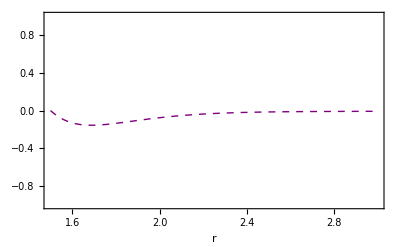

```mathematica
Plot[G3[r],{r,1.5,3},Frame->True, PlotRange->{-1,1},FrameLabel->{Style[" r ",Large,Black]}, PlotStyle->{{Purple, Thick, Dashed},{Purple, Thick,Dashed}}, FrameLabel->Automatic]
```